```mathematica
SetSystemOptions["CheckMachineUnderflow"->False];
bsearchMax=Compile[{{list,_Complex,1},{elem,_Real}},Block[{n0=1,n1=Length[list],m=0},While[n0≤n1,m=Floor[(n0+n1)/2];
If[list[[m]]==elem,While[m≥n0&&list[[m]]==elem,m--];Return[m+1]];
If[list[[m]]<elem,n0=m+1,n1=m-1]];
If[list[[m]]>elem,m,m+1]],RuntimeAttributes->{Listable},CompilationTarget->"C"];
```

# Spiking neural net simulator

## Model equations

## Single neurons - Conductance based adaptive Integrate-and-fire (CAdEx)

https://doi.org/10.1101/842823

V_i'[t]==1/Cm_i(gl_i*(El_i-V_i[t]) +gl_i*ΔT_i*E^((V_i[t]-VT_i)/ΔT_i)+gA_i[t]*(Ea_i-V_i[t])e+ Isyn_i+Iapp_i),
gA_i'[t]==(Ga_i/(1+E^((Va_i-V_i[t])/Δa_i))-gA_i[t])/τa_i,

## Initialization

Main 2 global variables include NeuronTypes and  SynapticParameterDistribution.
NeuronTypes is a list of Associations describing the properties for each distinct cell type in the network. Properties include the number of neurons of each type, their parameter distributions and some text description

```mathematica
NeuronTypes=Flatten@({{Association[

"Number"->10,
"Name"-> "Pyramidal Neuron",
"Cm"-> NormalDistribution[500,50],
"gl"-> NormalDistribution[3,0.5],
"El"-> NormalDistribution[-60,3],
"ΔT"-> NormalDistribution[3,0.5],
"VT"-> NormalDistribution[-50,2],
"Ea" -> NormalDistribution[-70,3],
"Ga"-> NormalDistribution[15,2],
"Va"-> NormalDistribution[-50,3],
"Δa"-> NormalDistribution[5,0.5],
"τa"-> NormalDistribution[200,20],
"δga"->  NormalDistribution[1.2,0.1],
"Vreset"->NormalDistribution[-55,2]
], Association[

"Number"-> 3,
"Name"-> "Basket Cell",
"Cm"-> NormalDistribution[90,10],
"gl"-> NormalDistribution[3,0.5],
"El"-> NormalDistribution[-60.5,3],
"ΔT"-> NormalDistribution[3,0.5],
"VT"-> NormalDistribution[-50,2],
"Ea" -> NormalDistribution[-70,3],
"Ga"-> NormalDistribution[15,2],
"Va"-> NormalDistribution[-50,3],
"Δa"-> NormalDistribution[0.5,0.05],
"τa"-> NormalDistribution[400,20],
"δga"->  NormalDistribution[0.07,0.01],
"Vreset"->NormalDistribution[-55,2]
]}});
SynapticParameterDistribution=({{Association[

"probability"->0.3,
"gsyn"-> NormalDistribution[2,0.5],
"Esyn"-> NormalDistribution[30,5],

"α"-> NormalDistribution[10,1],
"β"-> NormalDistribution[3,0.5],
"τx" -> NormalDistribution[10,2],
"δX"-> NormalDistribution[1,0.1],
"Source"-> "Pyramidal",
"Target"-> "Pyramidal",
"Description"-> "Fast excitatory AMPA synapse"
], Association[

"probability"-> 0.3,
"gsyn"-> NormalDistribution[2,0.5],
"Esyn"-> NormalDistribution[30,5],

"α"-> NormalDistribution[10,1],
"β"-> NormalDistribution[3,0.5],
"τx" -> NormalDistribution[10,2],
"δX"-> NormalDistribution[1,0.1],
"Source"-> "Pyramidal",
"Target"-> "Basket",
"Description"-> "Fast excitatory AMPA synapse"
]}, {Association[

"probability"-> 0.1,
"gsyn"-> NormalDistribution[10,3],
"Esyn"-> NormalDistribution[-90,5],

"α"-> NormalDistribution[10,1],
"β"-> NormalDistribution[3,0.5],
"τx" -> NormalDistribution[10,2],
"δX"-> NormalDistribution[1,0.1],
"Source"-> "Basket",
"Target"-> "Pyramidal",
"Description"-> "Fast inhibitory GABAa synapse"
], Association[

"probability"-> 0.4,
"gsyn"-> NormalDistribution[10,3],
"Esyn"-> NormalDistribution[-90,5],

"α"-> NormalDistribution[10,1],
"β"-> NormalDistribution[3,0.5],
"τx" -> NormalDistribution[10,2],
"δX"-> NormalDistribution[1,0.1],
"Source"-> "Basket",
"Target"-> "Basket",
"Description"-> "Fast inhibitory GABAa synapse"
]}});

SimulationTime = 1000;
```

## Creating network topology

GetConnectionMatrix creates a random Boolean matrix with dimensions {N,N}, where N - total number of neurons in the network 
a_(i,j) = = 1 means that neuron i synapses onto neuron j

```mathematica
GetConnectionMatrix[NeuronTypeNumbers_,probabilityMatrix_]:=
ArrayFlatten[
Transpose[
Table[
RandomVariate[BernoulliDistribution[probabilityMatrix[[col,row]]],{NeuronTypeNumbers[[col]],NeuronTypeNumbers[[row]]}],
{row,1,Length@NeuronTypeNumbers},{col,1,Length@NeuronTypeNumbers}],
1<->2]]*Mod[1+IdentityMatrix[Total@NeuronTypeNumbers],2];
```

PlotConnections plots creates a graph plot based on the adjacency matrix and the neuronal types distribution

```mathematica
PlotConnections[NeuronTypeNumbers_,adjacencyMatrix_]:=Module[{colors},
SeedRandom[70];
colors={RGBColor[0.8200000000000001, 0.19, 0.5],RGBColor[0.74, 1, 0.58],RGBColor[0, 0.51, 1]};
SeedRandom[];
Legended[
GraphPlot[AdjacencyGraph@adjacencyMatrix,
VertexStyle->Thread[Rule[
Range[Total@NeuronTypeNumbers],
Flatten@Table[Table[colors[[type]],{i,1,NeuronTypeNumbers[[type]]}],{type,1,Length@NeuronTypeNumbers}]]],VertexLabels->"Name"],
PointLegend[colors,StringReplace[Map[ToString,Reverse[Values@NeuronTypes[[All,{"Number","Name"}]],2]],{"{"->" ","}"->" "}]]]]
```

## Network Visualization

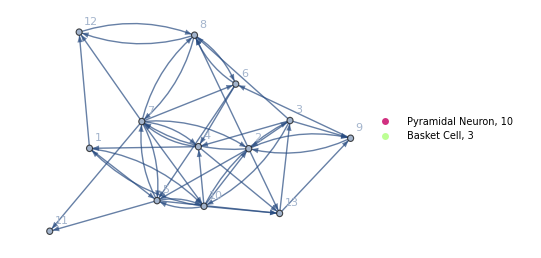

```mathematica
NetworkAdjacencyMatrix = GetConnectionMatrix[NeuronTypes[[All,"Number"]],SynapticParameterDistribution[[All,All,"probability"]]];

networkGraph =PlotConnections[
NeuronTypes[[All,"Number"]],
NetworkAdjacencyMatrix]
```

## Modelling neurons

General equation for a single neuron and a list of parameters need for each neuron

```mathematica
NeuronParameterList = {Cm,gl,El,ΔT,VT,Ea,Ga,Va,Δa,τa,δga,Vreset};
GenericNeuronEquation={
Subscript[V, i]'[t]==(Subscript[gl, i]*(Subscript[El, i]-Subscript[V, i][t]) +Subscript[gl, i]*Subscript[ΔT, i]*E^((Subscript[V, i][t]-Subscript[VT, i])/Subscript[ΔT, i])+Subscript[gA, i][t]*(Subscript[Ea, i]-Subscript[V, i][t])+ Subscript[Isyn, i]+Subscript[Iapp, i])/Subscript[Cm, i],
Subscript[gA, i]'[t]==(Subscript[Ga, i]/(1+E^((Subscript[Va, i]-Subscript[V, i][t])/Subscript[Δa, i]))-Subscript[gA, i][t])/Subscript[τa, i],
Subscript[V, i][0]==Subscript[El, i],
Subscript[gA, i][0]==0,
Subscript[event, i]
};
```

NeuronParameterValues is a set of rules for generating parameters for individual neurons, based on the distribution

```mathematica
NeuronParameterValues=Map[Thread,
Thread[Rule[
Table[Subscript[parameter, j],{parameter,NeuronParameterList},{j,1,Total@NeuronTypes[[All,"Number"]]}],
Table[
Flatten@Table[Table[RandomVariate@NeuronTypes[[type,ToString@parameter]],{i,1,NeuronTypes[[All,"Number"]][[type]]}],{type,1,Length@NeuronTypes[[All,"Number"]]}]
,{parameter,NeuronParameterList}]
]],1];
Grid[NeuronParameterValues[[All,1;;3]],Frame->All,Background->RGBColor[0.99, 1, 0.89, 0.78],ItemStyle->Directive[15]]
```

Cm_1→504.517 | Cm_2→483.917 | Cm_3→487.766
gl_1→3.31908 | gl_2→2.85639 | gl_3→2.76735
El_1→-55.3631 | El_2→-59.8433 | El_3→-56.1959
ΔT_1→2.61161 | ΔT_2→3.65717 | ΔT_3→3.1042
VT_1→-49.7127 | VT_2→-43.1932 | VT_3→-52.7256
Ea_1→-70.7676 | Ea_2→-72.8296 | Ea_3→-70.6804
Ga_1→12.3216 | Ga_2→11.5383 | Ga_3→15.7421
Va_1→-50.4714 | Va_2→-54.8897 | Va_3→-53.193
Δa_1→5.33002 | Δa_2→5.69741 | Δa_3→4.97332
τa_1→179.842 | τa_2→182.608 | τa_3→205.538
δga_1→1.29819 | δga_2→1.29628 | δga_3→1.14685
Vreset_1→-55.4986 | Vreset_2→-56.6215 | Vreset_3→-56.8101

## Modelling synapses

## Synaptic current equations

SymbolicSynapticCurrentRules is a set of symbolic rules to replace I_syn in the neuron equation. Generated based on the network connectivity

```mathematica
SynapseParameterList = {Esyn,gsyn,α,β,τx,δX};

SymbolicSynapticCurrentRules = Table[Subscript[Isyn, i]-> NetworkAdjacencyMatrix[[All,i]].Table[Subscript[gsyn, j,i]*Subscript[S, j,i][t]*(Subscript[Esyn, j,i]-Subscript[V, i][t]),{j,1,Total@NeuronTypes[[All,"Number"]]}],{i,1,Total@NeuronTypes[[All,"Number"]]}];

Column[SymbolicSynapticCurrentRules[[1;;3]],Frame->All,Background->RGBColor[0.99, 0.96, 1, 0.81],ItemStyle->Directive[15]]
```

Isyn_1→gsyn_(4,1) (Esyn_(4,1)-V_1[t]) S_(4,1)[t]+gsyn_(10,1) (Esyn_(10,1)-V_1[t]) S_(10,1)[t]
Isyn_2→gsyn_(3,2) (Esyn_(3,2)-V_2[t]) S_(3,2)[t]+gsyn_(7,2) (Esyn_(7,2)-V_2[t]) S_(7,2)[t]+gsyn_(9,2) (Esyn_(9,2)-V_2[t]) S_(9,2)[t]+gsyn_(10,2) (Esyn_(10,2)-V_2[t]) S_(10,2)[t]
Isyn_3→gsyn_(10,3) (Esyn_(10,3)-V_3[t]) S_(10,3)[t]+gsyn_(13,3) (Esyn_(13,3)-V_3[t]) S_(13,3)[t]

## Parameters for each individual synapse

SynapticParameterValues - a NxN matrix of associations for parameters of each individual synapse.
Parameters are based on the distributions described in the global variable SynapticParameterDistribution

```mathematica
SynapticParameterValues=
Map[Thread,
Map[Thread,
Thread[Rule[
Table[
Table[Subscript[parameter, j,i],{parameter,SynapseParameterList}],
{j,1,Total@NeuronTypes[[All,"Number"]]},
{i,1,Total@NeuronTypes[[All,"Number"]]}],

ArrayFlatten@Table[
Table[
Table[
RandomVariate[SynapticParameterDistribution[[col,row]][ToString@parameter]],
{parameter,SynapseParameterList}]
,
{j,1,NeuronTypes[[col,"Number"]]},
{i,1,NeuronTypes[[row,"Number"]]}],
{col,1,Length@NeuronTypes},
{row,1,Length@NeuronTypes}
]
]]
],{2}];

Grid[SynapticParameterValues[[1;;4,1;;4]],Frame->All,Background->RGBColor[1., 0.9, 0.93, 0.74]]
```

{Esyn_(1,1)→24.7258,gsyn_(1,1)→1.62575,α_(1,1)→9.78277,β_(1,1)→2.92067,τx_(1,1)→8.1044,δX_(1,1)→0.983266} | {Esyn_(1,2)→26.8153,gsyn_(1,2)→1.86638,α_(1,2)→8.58794,β_(1,2)→3.11482,τx_(1,2)→11.4496,δX_(1,2)→0.917441} | {Esyn_(1,3)→31.0891,gsyn_(1,3)→1.23928,α_(1,3)→10.1277,β_(1,3)→2.86973,τx_(1,3)→10.9071,δX_(1,3)→0.84878} | {Esyn_(1,4)→40.0522,gsyn_(1,4)→1.98596,α_(1,4)→10.8851,β_(1,4)→3.26335,τx_(1,4)→8.20531,δX_(1,4)→0.993611}
{Esyn_(2,1)→21.3019,gsyn_(2,1)→1.73448,α_(2,1)→8.86888,β_(2,1)→3.12089,τx_(2,1)→12.5694,δX_(2,1)→0.902361} | {Esyn_(2,2)→22.1379,gsyn_(2,2)→2.42938,α_(2,2)→9.33783,β_(2,2)→3.14972,τx_(2,2)→11.3777,δX_(2,2)→0.856562} | {Esyn_(2,3)→25.4475,gsyn_(2,3)→2.19257,α_(2,3)→10.3065,β_(2,3)→2.30615,τx_(2,3)→8.84063,δX_(2,3)→0.812859} | {Esyn_(2,4)→33.8869,gsyn_(2,4)→1.85449,α_(2,4)→9.87581,β_(2,4)→2.2997,τx_(2,4)→14.2754,δX_(2,4)→0.940681}
{Esyn_(3,1)→27.9674,gsyn_(3,1)→1.91765,α_(3,1)→11.3948,β_(3,1)→2.97059,τx_(3,1)→9.99009,δX_(3,1)→1.11846} | {Esyn_(3,2)→28.5557,gsyn_(3,2)→2.00631,α_(3,2)→8.46489,β_(3,2)→2.99078,τx_(3,2)→12.479,δX_(3,2)→1.15707} | {Esyn_(3,3)→36.5938,gsyn_(3,3)→1.99044,α_(3,3)→10.7507,β_(3,3)→3.42415,τx_(3,3)→8.76872,δX_(3,3)→1.02504} | {Esyn_(3,4)→28.6968,gsyn_(3,4)→2.20877,α_(3,4)→8.32833,β_(3,4)→2.99098,τx_(3,4)→8.35769,δX_(3,4)→1.0387}
{Esyn_(4,1)→29.3706,gsyn_(4,1)→2.5043,α_(4,1)→8.14899,β_(4,1)→4.56152,τx_(4,1)→8.8216,δX_(4,1)→1.1449} | {Esyn_(4,2)→29.4885,gsyn_(4,2)→2.14281,α_(4,2)→11.1299,β_(4,2)→3.35227,τx_(4,2)→10.1306,δX_(4,2)→0.858604} | {Esyn_(4,3)→22.9531,gsyn_(4,3)→1.83149,α_(4,3)→10.4481,β_(4,3)→2.11334,τx_(4,3)→7.43348,δX_(4,3)→1.04349} | {Esyn_(4,4)→29.4761,gsyn_(4,4)→3.15695,α_(4,4)→10.361,β_(4,4)→2.41878,τx_(4,4)→9.0693,δX_(4,4)→1.02285}

## Generating the system of Differential Equations

Generating necessary equations for S_(i,j) and X_(i,j) based on adjacency matrix

```mathematica
EquationsForS=Flatten@Pick[
Table[Subscript[S, i,j]'[t]==Subscript[α, i,j]*Subscript[X, i,j][t]*(1-Subscript[S, i,j][t])-Subscript[β, i,j]*Subscript[S, i,j][t],{i,1,Total@NeuronTypes[[All,"Number"]]},{j,1,Total@NeuronTypes[[All,"Number"]]}],
NetworkAdjacencyMatrix,1];

EquationsForX=Flatten@Pick[Table[Subscript[X, i,j]'[t]==(-Subscript[X, i,j][t])/Subscript[τx, i,j],{i,1,Total@NeuronTypes[[All,"Number"]]},{j,1,Total@NeuronTypes[[All,"Number"]]}],NetworkAdjacencyMatrix,1];

InitialConditionsX = Flatten@Pick[Table[Subscript[X, i,j][0]==0,{i,1,Total@NeuronTypes[[All,"Number"]]},{j,1,Total@NeuronTypes[[All,"Number"]]}],NetworkAdjacencyMatrix,1];

InitialConditionsS= Flatten@Pick[Table[Subscript[S, i,j][0]==0,{i,1,Total@NeuronTypes[[All,"Number"]]},{j,1,Total@NeuronTypes[[All,"Number"]]}],NetworkAdjacencyMatrix,1];
```

Generating equations for synaptic actions of each neuron (also based on the connectivity)

```mathematica
EventRules =Table[
With[{num=num},
Subscript[event, num]-> action[Subscript[V, num][t]>-20,
{Hold@Sow[{t,num}],Subscript[V, num][t]-> Subscript[Vreset, num],Subscript[gA, num][t]-> Subscript[gA, num][t] +Subscript[δga, num]}
~Join~
 Table[Subscript[X, num,j][t]-> Subscript[X, num,j][t]+Subscript[δX, num,j],{j,Pick[Range[Total@NeuronTypes[[All,"Number"]]],NetworkAdjacencyMatrix[[num]],1]}]
]],{num,Total@NeuronTypes[[All,"Number"]]}];
```

Equations for applied currents

```mathematica
AppliedCurrents = Table[Subscript[Iapp, i]-> RandomReal[{20,250}],{i,1,Total@NeuronTypes[[All,"Number"]]}];
```

Constructing and solving the main DE system

```mathematica
MainDESystem = 
Join[
Flatten@Table[GenericNeuronEquation,{i,1,Total@NeuronTypes[[All,"Number"]]}]/.Dispatch@EventRules/.Dispatch@SymbolicSynapticCurrentRules,
EquationsForS,EquationsForX,InitialConditionsS,InitialConditionsX]/.Dispatch[AppliedCurrents]/.Dispatch[Flatten@SynapticParameterValues]/.Dispatch[Flatten@NeuronParameterValues]/.action->WhenEvent;

VariablesToSolveFor = Table[Subscript[V, i],{i,1,Total@NeuronTypes[[All,"Number"]]}];
reportTime=AbsoluteTiming[{voltages,spikes} =Reap@ NDSolveValue[Simplify@MainDESystem,VariablesToSolveFor,{t,0,SimulationTime}];];
spikes=Flatten[spikes,1];
```

## Plotting results

Helper functions for faster time-series generation

```mathematica
bsearchMax=Compile[{{list,_Complex,1},{elem,_Real}},Block[{n0=1,n1=Length[list],m=0},While[n0≤n1,m=Floor[(n0+n1)/2];
If[list[[m]]==elem,While[m≥n0&&list[[m]]==elem,m--];Return[m+1]];
If[list[[m]]<elem,n0=m+1,n1=m-1]];
If[list[[m]]>elem,m,m+1]],RuntimeAttributes->{Listable},CompilationTarget->"C"];

multiInsert2[list_,val_,pos_]/;Length@val==Length@pos:=Module[{new,start,end,offset,n1,n2},{n1,n2}=Length/@{list,val};
new=ConstantArray[0,n1+n2];
start=Prepend[pos,1];
end=Append[pos-1,n1];
offset=Range[0,n2];
MapThread[new[[#;;#2]]=list[[#3;;#4]];&,{offset+start,offset+end,start,end}];
new[[pos+Range[0,n2-1]]]=val;
new];

SelectSpikesByNumber[n_]:=First/@Select[spikes,Last[#1]==n&];
```

A function to plot equal spikes for selected neurons

```mathematica
PlotBeautifulSpikes[neuronIDs_,T_]:=Module[{data,pos,spikeTimes},
Show@@
Table[
spikeTimes=SelectSpikesByNumber[k];
data=Table[t,{t,0,T,2}];
pos=Table[bsearchMax[data,time],{time,spikeTimes}];
ListLinePlot[multiInsert2[
Table[{t,voltages[[k]][t]},{t,0,T,2}],
Table[{j,20},{j,spikeTimes}],
pos],PlotRange->{-90,20},PlotStyle->RandomColor[],PlotLegends->{k}]
,{k,neuronIDs}]
]
```

```mathematica
spikePlot=PlotBeautifulSpikes[Range[Total@NeuronTypes[[All,"Number"]]],SimulationTime];
```

## Report generation

-Graphics-

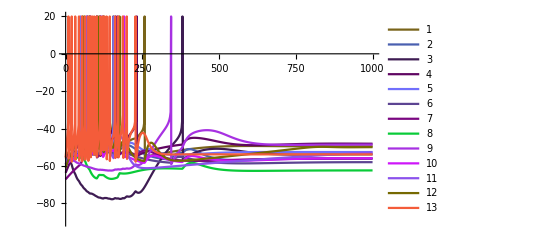

```mathematica
(*GenerateDocument[File["/Users/artem/Documents/Wolfram Mathematica/reportTemplate.nb"],
Association[
"Graph"-> networkGraph,
"Spikes"-> spikePlot,
"NumberOfDEs"->2* Total@NeuronTypes[[All,"Number"]] + 2*Total@Total@NetworkAdjacencyMatrix,
"time"->First@ reportTime
]]*)

networkGraph
spikePlot
```